## Example 8.3

```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
SetOptions[Plot,Axes->False,Frame->True,BaseStyle->{FontSize->16}];
```

```mathematica
<<VariationalMethods`
```

```mathematica
L = 1/2*m*(R^2*ω^2+l^2*θ'[t]^2+2*R*l*ω*θ'[t]*Sin[θ[t]-ω*t])-m*g*(R*Sin[ω*t]-l*Cos[θ[t]]);
```

```mathematica
euler=EulerEquations[ L,θ[t],t]//FullSimplify
```

l m (-R ω^2 Cos[t ω-θ[t]]+g Sin[θ[t]]+l θ''[t])==0

```mathematica
ode=euler/.{R->0.2,ω->2.5,l->1.0,g->9.8};
```

```mathematica
soln=NDSolve[{ode,θ[0]==1,θ'[0]==0},θ[t],{t,0,20}];
```

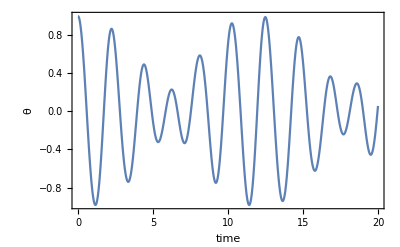

```mathematica
Plot[θ[t]/.soln,{t,0,20},FrameLabel->{"time","θ"}]
```

## Example 8.4

```mathematica
Remove["Global`*"]
```

```mathematica
<<VariationalMethods`
```

```mathematica
L = 1/2*m*(r'[t]^2+r[t]^2ω^2+4*r[t]^2*a^2*r'[t]^2)-m*g*a*r[t]^2
```

-a g m r[t]^2+1/2 m (ω^2 r[t]^2+r'[t]^2+4 a^2 r[t]^2 r'[t]^2)

```mathematica
euler=EulerEquations[ L,r[t],t]
```

-m (r[t] (2 a g-ω^2+4 a^2 r'[t]^2)+r''[t]+4 a^2 r[t]^2 r''[t])==0

```mathematica
Solve[euler,a,Assumptions->{r'[t]==0,r''[t]==0}][[1]]
```

{a→ω^2/(2 g)}

## Example 8.5

```mathematica
Remove["Global`*"]
```

```mathematica
<<VariationalMethods`
```

```mathematica
L =1/2*M*x1'[t]^2+1/2*m*(x1'[t]^2+x2'[t]^2+2*x1'[t]*x2'[t]*Cos[θ])-m*g*(l-x2[t])*Sin[θ];
```

```mathematica
euler=EulerEquations[ L,{x1[t],x2[t]},t]//FullSimplify
```

{(m+M) x1''[t]+m Cos[θ] x2''[t]==0,g m Sin[θ]==m (Cos[θ] x1''[t]+x2''[t])}

```mathematica
Solve[euler,{x1''[t],x2''[t]}][[1]]//FullSimplify
```

{x1''[t]→(g m Sin[2 θ])/(-m-2 M+m Cos[2 θ]),x2''[t]→-(2 g (m+M) Sin[θ])/(-m-2 M+m Cos[2 θ])}

## Example 8.7

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[Plot,Axes->False,Frame->True,BaseStyle->{FontSize->16}];
```

```mathematica
l=1.0;
m=1.0;
g=9.8;
```

```mathematica
soln=NDSolve[{θ'[t]==pθ[t]/(m l^2),pθ'[t]==-m g l Sin[θ[t]],θ[0]==3.0,pθ[0]==0},{θ,pθ},{t,0,20}];
```

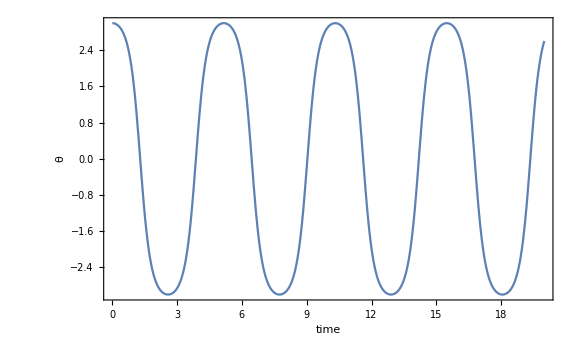

```mathematica
Plot[θ[t]/.soln,{t,0,20},BaseStyle->{Black,Bold,FontSize->22},Frame->True,Axes->False,FrameLabel->{"time","θ"},ImageSize->Large]
```

## Example 8.9

```mathematica
Remove["Global`*"]
```

```mathematica
SetOptions[ContourPlot,BaseStyle->{FontSize->16}];
```

```mathematica
l=1.0;
m=1.0;
g=9.8;
```

```mathematica
H[q_,p_]:=p^2/(2m l^2)-m g l Cos[q];
contour1=H[0.5,0];
contour2=H[2.0,0];
contour3=H[π,0];
contour4=H[π,4.43];
contour5=H[π,6.26];
```

```mathematica
contourList={contour1,contour2,contour3,contour4,contour5};
```

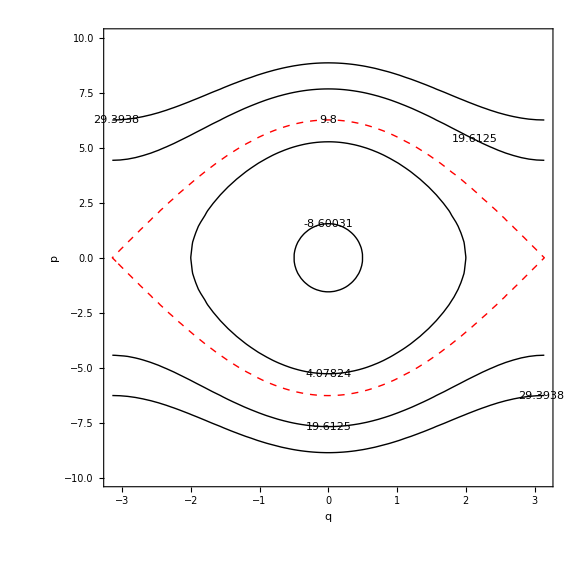

```mathematica
ContourPlot[H[q,p],{q,-π,π},{p,-10,10},ContourShading->None,Contours->contourList,ContourStyle->{Bold,Black, {Red,Dashed},Black,Black},FrameLabel->{"q","p"},ContourLabels->True]
```